```mathematica
Clear[x]
Table[{Floor[x/n],Ceiling[x/n]},{n,1,10}]//Flatten
```

{Floor[x],Ceiling[x],Floor[x/2],Ceiling[x/2],Floor[x/3],Ceiling[x/3],Floor[x/4],Ceiling[x/4],Floor[x/5],Ceiling[x/5],Floor[x/6],Ceiling[x/6],Floor[x/7],Ceiling[x/7],Floor[x/8],Ceiling[x/8],Floor[x/9],Ceiling[x/9],Floor[x/10],Ceiling[x/10]}

```mathematica
Table[{i->{i+1}},{i,1,20,2}]
```

{{1→{2}},{3→{4}},{5→{6}},{7→{8}},{9→{10}},{11→{12}},{13→{14}},{15→{16}},{17→{18}},{19→{20}}}

```mathematica
xx=50
```

50

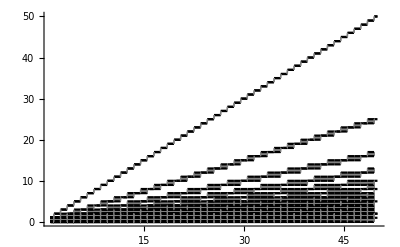

```mathematica
Plot[Evaluate[Table[{Floor[Floor[x+1/2]/n],Ceiling[Floor[x+1/2]/n]},{n,1,xx}]//Flatten],{x,1,xx},Filling->Table[{i->{i+1}},{i,1,2xx,2}],PlotStyle->Black,FillingStyle->Gray,PlotRange->All]
```

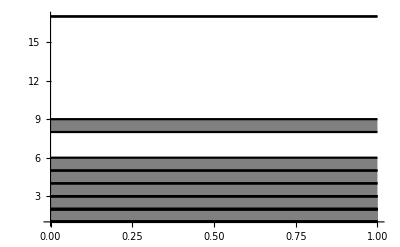

```mathematica
Plot[Evaluate[Table[{Floor[Floor[x+1/2]/n],Ceiling[Floor[x+1/2]/n]},{n,1,xx}]//Flatten],{x,1,xx},Filling->Table[{i->{i+1}},{i,1,2xx,2}],PlotStyle->Black,FillingStyle->Gray,PlotRange->All]
```

-Graphics-